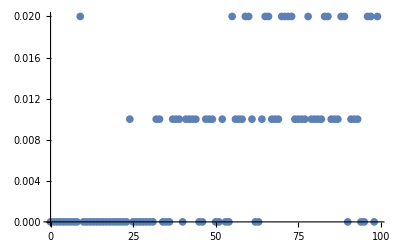

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "name"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
ListPlot[data]
```